# Lecture 6 - Energy

### A Puzzle...

Recall that the Taylor series of a function f[x] about the point x=a equals

∑_(n=0)^∞ (f^(n)[a])/(n!)(x-a)^n=f[a]+f'[a]/(1!)(x-a)+f''[a]/(2!)(x-a)^2+f'''[a]/(3!)(x-a)^3+···

Examples
1. What is a Taylor series useful for?
2. What is special about the Taylor series around a local minimum or maximum?
3. Prove that ⅇ^x,Cos[x],and Sin[x] are all exactly equal to their Taylor series. This is not true of functions in general.

Solutions
1. One useful function of a Taylor series is that allows you to approximate the function f[x] around the region x=a, regardless of how complicated f[x] is! As a simple example, here we approximate Sin[x] with successively higher orders of the Taylor series.

```mathematica
centerPlot@Manipulate[
series=Table[Normal[Series[Sin[x],{x,0,n}]],{n,1,jj,2}];
Show[Plot[series,{x,0,4Pi},PlotRange->{-1,1},ImageSize->250],Plot[Sin[x],{x,0,4Pi},PlotStyle->{Black,Thin,Dashed}]]
,{{jj,15,"order"},1,30,2,Appearance->"Open"}]
```

But the power of the Taylor series comes in its ability to approximate any function f[x] around any point. For example, suppose for some physics problem you need to compute how Sin[ⅇ^(x^2)-1] behaves around x=0. The Taylor series equals Sin[ⅇ^(x^2)-1]≈x^2+x^4/2+O[x^5]; therefore, very close to x=0, Sin[ⅇ^(x^2)-1]≈x^2 and we can replace a very complicated function by a simple quadratic function.

Similarly, when we make the small angle approximations Cos[x]≈1 and Sin[x]≈x around x=0, we are expanding these functions to lowest order in their Taylor series.

2. If a is a local minimum or maximum, f'[a]=0 and therefore around x=a,

f[x]≈f[a]+f''[a]/(2!)(x-a)^2+O[(x-a)^3]

so we can replace f[x] by a quadratic function (typically you want one additional term beyond the 0^th order constant).

3. One of the defining properties of ⅇ^x is that it equals its own derivative. If the Taylor series of ⅇ^x also equals its own derivative, then the Taylor series must equal c_1 ⅇ^x (you can prove this to yourself by solving the differential equation y'[x]=y[x]). The Taylor series of ⅇ^x equals

∑_(j=0)^∞ x^j/(j!)=1+x/(1!)+x^2/(2!)+x^3/(3!)+···

so its derivative equals

ⅆ/ⅆx[∑_(j=1)^∞ x^j/(j!)]=∑_(j=0)^∞ (j x^(j-1))/(j!)=∑_(j=1)^∞ x^(j-1)/((j-1)!)=∑_(j=0)^∞ x^j/(j!)

Thus the Taylor series must equal c_1 ⅇ^x and plugging in x=0 shows that c_1=1, proving that the Taylor series of ⅇ^x equals ⅇ^x exactly!

This does not hold for general functions, but it does hold for Sin[x] and Cos[x], as you can prove to yourself analogously to the method shown above. Therefore, another definition of these trig functions equals

Sin[x]=x-x^3/(3!)+x^5/(5!)-···=∑_(j=0)^∞ (-1)^j x^(2j+1)/((2j+1)!)
Cos[x]=1-x^2/(2!)+x^4/(4!)-···=∑_(j=0)^∞ (-1)^j x^(2j)/((2j)!)

### Energy

#### Energy in 1D

Consider a one dimensional force F[x] acting in the x̂ direction which only depends upon position. We can write

F[x]=m a
=m ⅆv/ⅆt
=m ⅆv/ⅆx ⅆx/ⅆt
=m v ⅆv/ⅆx

Multiplying both sides by ⅆx and integrating (say x ranges from x_0 to x and v from v_0 to v (note that technically our integration variables should be x' and v', but that notation is cumbersome)),

1/2 m v^2=E+∫_x_0^x F[x]ⅆx

where E is a constant that depends on x_0 and v_0. Defining

V[x]≡-∫_x_0^x F[x]ⅆx

we find

1/2 m v^2+V[x]=E

We call the first term (1/2 m v^2) the kinetic energy and the second term (V[x]) the potential energy. If we consider the particle at two different positions x_1 and x_2, the constant E must be the same in the above equation for both positions and hence we find

1/2 m v[x_2]^2-1/2 m v[x_1]^2=V[x_1]-V[x_2]
=∫_x_1^x_2 F[x]ⅆx
≡W

where we have defined this last integral as the work (W) of moving the particle from x_1 to x_2.

Given any potential V[x], the force F[x]=-ⅆV/ⅆx can be found by differentiation.

Example
A particle with mass m moves straight up against gravity (in the z-direction). What is the potential V[z] the particle feels? Given that the particle starts with velocity v on the ground, how high will it reach before it falls?

Solution
Using the ground as the reference point,

V[z]=-∫_0^z F[z]ⅆz=-∫_0^z (-m g)ⅆz=m g z

We know 1/2 m v^2+V[z]=E is a constant for the motion of the particle. When the particle is on the ground, its total energy equals

E=1/2 m v^2

When the particle is at its maximum height z_max, its velocity is v=0 and its potential energy equals V[z_max]=m g z_max, which we equate to the total energy,

E=m g z_max

Setting these two relations equal to each other yields

z_max=v^2/(2 g)

Of course, this is the same result we found when using force analysis (in Lecture 3). □

Note that the value of V[x] does not have a physical meaning, since it depends on the reference point x_0. Only differences in potential matter! For example, if a mass m moves up and down against gravity, then when it is at height h we could say that its potential is m g h relative to the ground or m g h+(10meters)g h relative to a reference point 10 meters below the ground. Both are correct, and as long as you maintain the same reference point throughout a problem, all physical quantities you measure will be the same. Typically, when dealing with gravity on Earth we assume the ground as the reference point; in various problems where particles go to infinity, we may choose ∞ as the reference point.

Example
A point mass m moves in 1D under the potential V[x] shown below. You are given an initial position x_0 and an initial velocity v_0 for the particle, from which you compute E=1/2 m v_0^2+V[x_0]. You then draw a horizontal line on your V[x] plot at height E. Describe the motion of m.

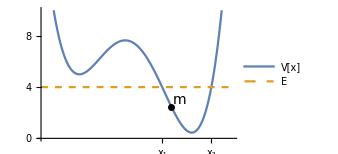

```mathematica
xVal=x/.Solve[x^2-3./2(x-2)^3+(x-3)^4==4,x][[3;;4]];
centerPlot@Show[
Plot[{x^2-1.5(x-2)^3+(x-3)^4,4},{x,1,6},PlotRange->{Automatic,{0,10}},PlotStyle->{Automatic,Dashed},PlotLegends->(font/@{"V[x]","E"}),Ticks->{{{xVal[[1]],font@"x_1"},{xVal[[2]],font@"x_2"}},None},ImageSize->250],
pnt={4.4,x^2-3./2(x-2)^3+(x-3)^4/.x->4.4};
Graphics[{PointSize[0.02],Point[pnt],Text[font["m"],pnt+{0.2,0.5}]}]
]
```

Solution
At the points where V[x]=E=1/2 m v^2+V[x], we must have v=0, indicating that the particle will have zero velocity. Looking at the particular values in the above graph, the force on the particle F[x]=-ⅆV/ⅆx will accelerate the particle back into the region x∈[x_1,x_2]. Furthermore, we know that for all points x∈(x_1,x_2) the velocity will not be zero. Therefore, the motion of the particle will be to move back and forth between x_1 and x_2 indefinitely.

If E was raised so that it just hits the local maximum of V[x] what is the resulting motion?

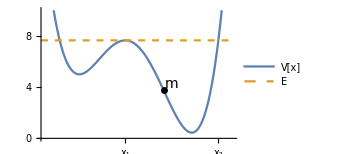

```mathematica
xVal=x/.Solve[x^2-3./2(x-2)^3+(x-3)^4==7.649738597363516,x][[3;;4]];
centerPlot@Show[
Plot[{x^2-1.5(x-2)^3+(x-3)^4,7.649738597363516},{x,1,6},PlotRange->{Automatic,{0,10}},PlotStyle->{Automatic,Dashed},PlotLegends->(font/@{"V[x]","E"}),Ticks->{{{xVal[[1]],font@"x_1"},{xVal[[2]],font@"x_2"}},None},ImageSize->250],
pnt={4.2,x^2-3./2(x-2)^3+(x-3)^4/.x->4.2};
Graphics[{PointSize[0.02],Point[pnt],Text[font["m"],pnt+{0.2,0.5}]}]
]
```

We would expect that the particle would head towards x_1 and eventually arrive there. When it does, not only will v=0 but also F[x]=-ⅆV/ⅆx=0 which implies that its acceleration is 0. Therefore, the particle will stay at x_1 forever. However, as the next example shows, the situation can be a little bit more complicated than that. □

#### Will it Reach?

Example 
A particle moves toward x=0 under the influence of a potential V[x]=-A(|x|)^n where A>0 and n>0. The particle has barely enough energy to reach x=0. For what values of n will it reach x=0 in a finite time?

Solution
The first step in any such problem is to understand what the potential looks like and get an intuitive feel for the motion.

```mathematica
centerPlot@Manipulate[Plot[-A*Abs[x]^n,{x,-10,10},ImageSize->230,AxesLabel->font/@{"x","V[x]"},PlotRange->{Automatic,{0,-10}}],{{A,0.1,font["A",Italic]},0.001,10},{{n,2,font["n",Italic]},0.001,10},Initialization:>(font[text_,size_Integer:14,opts___]:=(Style[text,size,FontFamily->"Times",opts]))]
```

Lets say the particle begins at x_0>0 at moves left with velocity v_0 towards the origin. What is the total energy of the particle? That the particle barely reaches the origin implies that its kinetic energy at the origin would be zero. Therefore, its total energy equals the potential energy at the origin,

E=V[0]=0

Conservation of energy (kinetic plus potential energy) at an arbitrary x yields

0=E=1/2 m v^2-A x^n

so that

ⅆx/ⅆt=v=-((2A)/m)^(1/2) x^(n/2)

Upon rearranging terms,

ⅆx/x^(n/2)=-((2A)/m)^(1/2)ⅆt

which we can integrate to find

∫_x_0^0 ⅆx/x^(n/2)=-∫_0^t ((2A)/m)^(1/2)ⅆt

(x_0)^(1-n/2)/(1-n/2)=((2A)/m)^(1/2)t

Note that the integral on the left-hand side only converges when n<2. For n≥2 the integral does not converge so the particle does not reach the origin in a finite amount of time. For example, a mass climbing up a triangle with just the right amount of energy would reach the peak in a finite amount of time, but a mass climbing up a circle would not (because at the top of a circle, the potential looks like a downwards parabola).

An exceptionally important special case is when a particle is climbing towards any local maximum (such as the one shown in the Example above). Suppose the local maximum occurs at x=x_max. Then V'[x_max]=0, and therefore the Taylor series of the potential at the local maximum is of the form V[x]≈V[x_max]-1/2 V''[x_max]x^2+··· so that the particle will take an infinite amount of time to reach the local maximum! □

#### Conservative Forces

For some forces, the work done depends on how the particle moves. Such is the case for forces that depend on t or v, because it then matters when or how quickly the particle goes from x_1 to x_2. A common example of such a force is friction. If you slide a brick across a table from x_1 to x_2, then the work done by friction equals -μ m g |x_2-x_1|. But if you slide the brick by wiggling it back and forth for an hour before you finally reach x_2, then the amount of negative work done by friction will be very large. Since friction always opposes the motion (i.e. friction lies along the direction -v⃗), the contributions to the W=∫F ⅆx integral are always negative, so there is never any cancellation. The result is therefore a large negative number.

We define a conservative force as one for which the work done on a particle between two given points is independent of how the particle makes the journey. For example, in one dimension, any force F[x] that only depends on the position x is conservative because the work

W=∫_x_1^x_2 F[x]ⅆx
=∫_x_1^x_2 m aⅆx
=∫_x_1^x_2 m ⅆv/ⅆt ⅆx
=∫_x_1^x_2 m ⅆv/ⅆx ⅆx/ⅆt ⅆx
=∫_x_1^x_2 m v ⅆv/ⅆx ⅆx
=1/2 m v[x_2]^2-1/2 m v[x_1]^2

only depends on the endpoints and is independent of how the particle moves. Although we can always define the work done by any force, we can only talk about potential energy associated with a force if the force is conservative.

Energy is conserved within a system when:

All forces are conservative

All entities that emit forces are part of your system

When condition 2 is not met, energy can either decrease (e.g., friction) or increase (e.g., a particle rolls into a fast moving stream and picks up velocity). For example, consider the following problem. Since there are no dissipative forces, the energy must be conserved if we consider the entire system. But what is that system?

#### Rotating Hemisphere

Example
A marble of mass m is deposited inside a hemispherical bowl of radius R, as shown in the figure. The bowl is then spun around its vertical axis with a constant angular velocity ω. The marble eventually settles at a distance r from the bowl’s vertical axis while rotating around that axis with the same angular velocity ω as the bowl itself. Is the energy of the mass conserved throughout its motion, and if not where does the energy come from?

```mathematica
centerPlot@-Graphics-
```

-Graphics-

Solution
Energy is not conserved. For example, suppose the particle starts off very near the bottom of the hemisphere where its velocity will be approximately 0 (since it is so close to the rotation axis ω⃗ and v⃗=r⃗×ω⃗). Therefore, its initial energy is approximately 0. Defining the bottom of the hemisphere as the reference point for our gravitational potential, we see that the particle will move outwards (in the rotated reference frame by the centrifugal force) until it settles at an equilibrium height. At this point, the gravitational potential energy will be m g h where h=R-√(R^2-r^2) while the kinetic energy will equal 1/2 m v^2 where v=ω r. Thus the mass will end up with an energy far larger than 0, and so energy is most certainly not conserved.

In this case, the extra energy come from whatever mechanism is maintaining a constant angular velocity ω. For as the particle moves outward, it becomes more and more difficult to rotate the hemisphere (think of how a baseball bat is harder to swing if you place a weight at the far end rather than if you place the same weight right near your grip (we will discuss this more rigorously once we learn about the moment of inertia)), and hence something must exert more force to keep the hemisphere rotating at ω. That extra force is what gives the mass its difference in energy. □

#### Energy in 3D

In 3D, Newton’s 2nd law becomes F⃗=m a⃗ where

F⃗=F_x x̂+F_y ŷ+F_z ẑ

and

a⃗=(ⅆ v_x)/ⅆt x̂+(ⅆ v_y)/ⅆt ŷ+(ⅆ v_z)/ⅆt ẑ
=(ⅆ v_x)/ⅆx ⅆx/ⅆt x̂+(ⅆ v_y)/ⅆy ⅆy/ⅆt ŷ+(ⅆ v_z)/ⅆz ⅆz/ⅆt ẑ
=v_x(ⅆ v_x)/ⅆx x̂+v_y(ⅆ v_y)/ⅆy ŷ+v_z(ⅆ v_z)/ⅆz ẑ

Thus writing Newton’s 2nd law component wise and rearranging, we obtain

F_x ⅆx=m v_x ⅆ v_x

F_y ⅆy=m v_y ⅆ v_y

F_z ⅆz=m v_z ⅆ v_z

Adding these three equations together,

F_x ⅆx+F_y ⅆy+F_z ⅆz=m (v_x ⅆ v_x+v_y ⅆ v_y+v_z ⅆ v_z)

Integrating from (x_0,y_0,z_0) to (x,y,z),

E+∫_x_0^x F_x ⅆx+∫_y_0^y F_y ⅆy+∫_z_0^z F_z ⅆz=1/2 m (v_x^2+v_y^2+v_z^2)=1/2 m v^2

where E is the constant of integration that we lovingly call energy. Note that the integral on the left-hand side may depend on the path of integration chosen (we will discuss this shortly). Denote ⅆ r⃗=ⅆx x̂+ⅆy ŷ+ⅆz ẑ so that the three integrals on the left-hand side can be compactly written as

∫_((r⃗)_0)^(r⃗) F⃗[r⃗']·ⅆr⃗'≡∫_x_0^x F_x ⅆx+∫_y_0^y F_y ⅆy+∫_z_0^z F_z ⅆz

Substituting this in,

E=1/2 m v^2-∫_((r⃗)_0)^(r⃗) F⃗[r⃗']·ⅆr⃗'

Just as in the 1D case, we now define the potential

V[r⃗]≡-∫_((r⃗)_0)^(r⃗) F⃗[r⃗']·ⅆr⃗'

so that we can write

E=1/2 m v^2+V[r⃗]

which is the 3D analog of the 1D conservation of energy equation that we found above.

#### Advanced Section: Defining a Potential

When we define V[r⃗]≡-∫_((r⃗)_0)^(r⃗) F⃗[r⃗']·ⅆr⃗' in 3D, we encounter the serious issue that the integral may be path-dependent. (This was not a problem in 1D provided that F[x] only depended upon x and not on v or t.) This is a serious problem, because if the integral is not path dependent, then we cannot talk about a potential and hence we cannot use conservation of energy (as, for example, we cannot in problems that have friction). Fortunately, the following theorem tells us exactly when a force F⃗[r⃗] gives rise to a potential V[r⃗] that is path independent.

But first, some mathematical notation. The Del operator OverVector[∇] is defined as

OverVector[∇]=∂/(∂x)x̂+∂/(∂y)ŷ+∂/(∂z)ẑ

Recall that a useful mnemonic for the cross product A⃗×B⃗ where A⃗=A_x x̂+A_y ŷ+A_z ẑ and B⃗=B_x x̂+B_y ŷ+B_z ẑ is given by

A⃗×B⃗=|x̂ | ŷ | ẑ
A_x | A_y | A_z
B_x | B_y | B_z|

Therefore, we find

OverVector[∇]×B⃗=|x̂ | ŷ | ẑ
∂/(∂x) | ∂/(∂y) | ∂/(∂z)
B_x | B_y | B_z|

which upon taking the "determinant" yields

OverVector[∇]×B⃗=((∂B_z)/(∂y)-(∂B_y)/(∂z))x̂+((∂B_x)/(∂z)-(∂B_z)/(∂x))ŷ+((∂B_y)/(∂x)-(∂B_x)/(∂y))ẑ

The vector OverVector[∇]×B⃗ is known as the curl of B⃗.

Theorem
A force F⃗[r⃗] gives rise to a potential V[r⃗]=-∫_((r⃗)_0)^(r⃗) F⃗[r⃗']·ⅆr⃗' that is path independent (and therefore well-defined) iff OverVector[∇]×F⃗=OverVector[0].

Proof
Consult David Morin’s book (Introduction to Classical Mechanics with Problems and Solutions) Theorem 4.2 for a proof. □

The curl of F⃗ can be visualized as the infinitesimal rotation of a very small object (but not a point particle) at every point in space. The direction of the curl is the axis of rotation - as determined by the right-hand rule - and the magnitude of the curl is the magnitude of rotation.

Example
Calculate the curl of F⃗[r⃗]=y x̂-x ŷ.

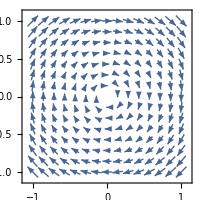

```mathematica
centerPlot@VectorPlot[{y,-x},{x,-1,1},{y,-1,1},ImageSize->200]
```

Solution
By inspection we can tell that this F⃗[r⃗] will generate a rotation in the -ẑ at all points in space (not just at the origin). Mathematically,

OverVector[∇]×F⃗=((∂F_z)/(∂y)-(∂F_y)/(∂z))x̂+((∂F_x)/(∂z)-(∂F_z)/(∂x))ŷ+((∂F_y)/(∂x)-(∂F_x)/(∂y))ẑ
=(-1-1)ẑ
=-2 ẑ

which means that every point in space would feel a rotation of the same magnitude characterized by an axis of rotation ω⃗=-2 ẑ. □

Example
Calculate the curl of F⃗[r⃗]=- ẑ (analogous to Earth’s gravitation).

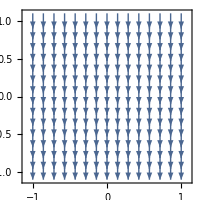

```mathematica
centerPlot@VectorPlot[{0,-1},{x,-1,1},{y,-1,1},ImageSize->200]
```

Solution
By inspection, this F⃗[r⃗] will not rotate any shape placed at any point in space (although it will translate, we are only considering rotations). Mathematically,

OverVector[∇]×F⃗=((∂F_z)/(∂y)-(∂F_y)/(∂z))x̂+((∂F_x)/(∂z)-(∂F_z)/(∂x))ŷ+((∂F_y)/(∂x)-(∂F_x)/(∂y))ẑ
=OverVector[0]

as expected. This tells us that the Earth’s gravitational gives rise to a path independent potential so we can use conservation of energy in such problems. □

Example
Calculate the curl of the central potential F⃗[r⃗]=F[r] r̂ (one such case is the gravitational potential of a planet governed by F⃗[r⃗]=-G (m_1 m_2)/r^2 r̂).

Solution
We cannot plot this potential, since F[r] can be any function of r. However, it is still helpful to just have a picture in your head of a specific potential.

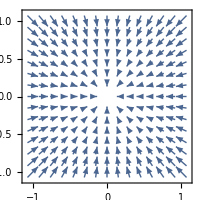

```mathematica
centerPlot@VectorPlot[{-x,-y},{x,-1,1},{y,-1,1},ImageSize->200]
```

With this in hand, let’s see what the math says. Writing

r̂=x/r x̂+y/r ŷ+z/r ẑ

which you can verify is both a unit vector and points in the radial direction, we can compute

(∂r)/(∂x)=(∂(x^2+y^2+z^2)^(1/2))/(∂x)=x/r

and similarly

(∂r)/(∂y)=y/r

(∂r)/(∂z)=z/r

Therefore, the z-component of OverVector[∇]×F⃗ equals

(∂F_y)/(∂x)-(∂F_x)/(∂y)=∂/(∂x)[F[r]y/r]-∂/(∂y)[F[r]x/r]
=F'[r]y/r(∂r)/(∂x)-F[r]y/r^2(∂r)/(∂x)-F'[r]x/r(∂r)/(∂y)+F[r]x/r^2(∂r)/(∂y)
=F'[r]y/r x/r-F[r]y/r^2 x/r-F'[r]x/r y/r+F[r]x/r^2 y/r
=0

By symmetry, the same result holds for the x- and y-components of OverVector[∇]×F⃗ and therefore OverVector[∇]×F⃗=OverVector[0], indicating that any central force corresponds to a path independent potential and hence permits conservation of energy. □

#### A Weird Wire

Example
A bead, under the influence of gravity, slides along a frictionless wire whose height is given by the function y[x]. Assume that at position (x,y)=(0,0) the wire is vertical and the bead passes this point with a given speed v_0 downward. What should the shape of the wire be (that is, what is y as a function of x) so that the vertical speed remains v_0 at all times?

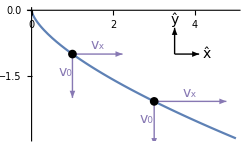

```mathematica
centerPlot@Show[
Plot[-x^(2/3),{x,0,5},Ticks->None,ImageSize->250],
pt1={x,-x^(2/3)}/.x->1;
pt2={x,-x^(2/3)}/.x->3;
vy=1;
vx1=√(-1.5*pt1[[2]]);
vx2=√(-1.5*pt2[[2]]);
Graphics[{{color3,Thick,Arrowheads[Medium],Arrow[{{pt1,pt1+{0,-vy}},{pt1,pt1+{vx1,0}},{pt2,pt2+{0,-vy}},{pt2,pt2+{vx2,0}}}],Text[font@"v_0",{-0.18,00.1}+Mean@{pt1,pt1+{0,-vy}}],Text[font@"v_0",{-0.18,00.1}+Mean@{pt2,pt2+{0,-vy}}],Text[font@"v_x",{0,0.2}+Mean@{pt1,pt1+{vx1,0}}],Text[font@"v_x",{0,0.2}+Mean@{pt2,pt2+{vx2,0}}]},{PointSize[0.025],Point[{pt1,pt2}]},directionVectors[{3.5,-1},6,False]}]
]
```

Solution
We orient positive velocities as up and to the right, as usual. We want for the downwards component of the velocity to remain -v_0 the entire time. By conservation of energy,

1/2 m v_0^2=1/2 m (v_x^2+v_0^2)+m g y

which yields

v_x=√(-2 g y)

The negative sign is good because y will be negative for all positive x values. The velocity v⃗=v_x x̂-v_0 ŷ must be parallel to the wire, and hence

ⅆy/ⅆx=-v_0/v_x=-v_0/(√(-2 g y))

Rearranging terms,

ⅈ y^(1/2)ⅆy=√-y ⅆy=-v_0/(√(2 g))ⅆx

Let’s not be alarmed by the fact that ⅈ=√-1 has appeared in the equation, as we know that it will have to drop out in the end. Integrating both sides,

2/3 ⅈ y^(3/2)=-v_0/(√(2 g))x+C

where the point (x,y)=(0,0) shows us that C=0. Note that on the left-hand side,

ⅈ y^(3/2)=ⅈ y y^(1/2)
=y √-y
=-(-y) √-y
=-(-y)^(3/2)

Thus the above equation becomes

2/3(-y)^(3/2)=v_0/(√(2 g))x

Some more simplifying yields

(-y)^(3/2)=(3 v_0 g)/(2 g)^(3/2)x

-y=(3 v_0 g x)^(2/3)/(2 g)

y=-(3 v_0 g x)^(2/3)/(2g)

which is the desired form y[x]. □

## Mathematica Initialization

```mathematica
(* Font size for all plots in this notebook *)
ft=16;
```

```mathematica
(* Primary colors for figures *)
colors={color1,color2,color3,color4,color5,color6}={ColorData[97][1],ColorData[97][10],ColorData[97][5],ColorData[97][6],ColorData[97][9],Lighter@ColorData[97][7]};
(* Secondar colors for backgrounds *)
backgroundColors={backgroundColor1}={RGBColor[0.99, 0.97432, 0.91748]};
```

```mathematica
Clear[font]
font[text_,size_Integer:14,opts___]:=(Style[text,size,FontFamily->"Times",opts])
```

```mathematica
$Assumptions=By>0&&Bz>0&&c>0&&0<ϕ<2π&&0≤ψ≤2π;
```

```mathematica
(* To make x̂-, ŷ-, and ẑ-direction vectors in a Graphics *)
Clear[directionVectors]
directionVectors[base_,size_:1,threeDimQ_:True]:={Black,Arrowheads[Small],Arrow[{{base,base+size{0.1,0}},{base,base+size{0,0.1}}}],Text[font@"x̂",base+size{0.13,0}],Text[font@"ŷ",base+size{0,0.13}],If[threeDimQ,{Arrow[{base,base+size{-0.05,-0.05}}],Text[font@"ẑ",base+size{-0.06,-0.065}]},Sequence@@{}]}
```